```mathematica
2f Integrate[t Sin[ω t],{t,0,1/f}]//Simplify
```

(2 (-ω Cos[ω/f]+f Sin[ω/f]))/ω^2

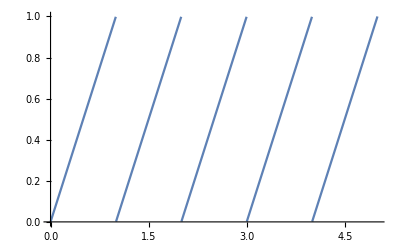

```mathematica
Plot[SawtoothWave[t],{t,0,5}]
```

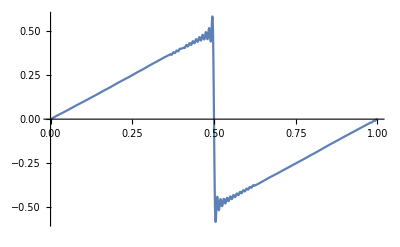

```mathematica
Plot[-1/π Sum[(-1)^k Sin[2π k φ]/k,{k,1,100}],{φ,0,1}]
```

```mathematica
Monitor[s1=Table[-1/π Sum[(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))(Sin[2π k 440./2^(1/12)t]/k+Sin[2π k 440./2^(6/12)t]/k+Sin[2π k 440./2^(9/12)t]/k),{k,1,50}],{t,1/44100.,1.5,1/44100.}];,t+0.]
```

```mathematica
Monitor[s2=Table[-1/π Sum[(-1)^k 0.5(Sin[2π k 440./2^(6/12)t]/k+Sin[2π k 440./2^(9/12)t]/k)+(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))Sin[2π k 440./2^(1/12)t]/k,{k,1,50}],{t,1/44100.,0.25,1/44100.}];,t+0.]
```

```mathematica
Monitor[s3=Table[-1/π Sum[(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))(Sin[2π k 440./2^(2/12)t]/k+Sin[2π k 440./2^(4/12)t]/k+Sin[2π k 440./2^(9/12)t]/k),{k,1,50}],{t,1/44100.,0.5,1/44100.}];,t+0.]
```

```mathematica
Monitor[s4=Table[-1/π Sum[(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))Sin[2π k 440./2^(1/12)t]/k+(-1)^k 0.5(Sin[2π k 440./2^(4/12)t]/k+Sin[2π k 440./2^(9/12)t]/k),{k,1,50}],{t,1/44100.,0.25,1/44100.}];,t+0.]
```

```mathematica
Monitor[s5=Table[-1/π Sum[(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))Sin[2π k 440./2^(-1/12)t]/k+(-1)^k 0.5(Sin[2π k 440./2^(4/12)t]/k+Sin[2π k 440./2^(9/12)t]/k),{k,1,50}],{t,1/44100.,0.75,1/44100.}];,t+0.]
```

```mathematica
Monitor[s6=Table[-1/π Sum[(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))Sin[2π k 440./2^(2/12)t]/k+(-1)^k 0.5(Sin[2π k 440./2^(4/12)t]/k+Sin[2π k 440./2^(9/12)t]/k),{k,1,50}],{t,1/44100.,0.25,1/44100.}];,t+0.]
```

```mathematica
Monitor[s7=Table[-1/π Sum[(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))Sin[2π k 440./2^(1/12)t]/k+(-1)^k 0.5(Sin[2π k 440./2^(4/12)t]/k+Sin[2π k 440./2^(9/12)t]/k),{k,1,50}],{t,1/44100.,0.25,1/44100.}];,t+0.]
```

```mathematica
Monitor[s8=Table[-1/π Sum[(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))(Sin[2π k 440./2^(4/12)t]/k+Sin[2π k 440./2^(8/12)t]/k)+(-1)^k 0.5 Sin[2π k 440./2^(1/12)t]/k,{k,1,50}],{t,1/44100.,1.5,1/44100.}];,t+0.]
```

```mathematica
Monitor[s9=Table[-1/π Sum[(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))(Sin[2π k 440./2^(4/12)t]/k+Sin[2π k 440./2^(8/12)t]/k)+(-1)^k 0.5 Sin[2π k 440./2^(1/12)t]/k,{k,1,50}],{t,1/44100.,0.25,1/44100.}];,t]
```

```mathematica
Monitor[s10=Table[-1/π Sum[(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))(Sin[2π k 440./2^(6/12)t]/k+Sin[2π k 440./2^(11/12)t]/k+Sin[2π k 440./2^(2/12)t]/k),{k,1,50}],{t,1/44100.,0.5,1/44100.}];,t]
```

```mathematica
Monitor[s11=Table[-1/π Sum[(-1)^k 0.5(Sin[2π k 440./2^(6/12)t]/k+Sin[2π k 440./2^(11/12)t]/k)+(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))Sin[2π k 440./2^(1/12)t]/k,{k,1,50}],{t,1/44100.,0.25,1/44100.}];,t]
```

```mathematica
Monitor[s12=Table[-1/π Sum[(-1)^k 0.5(Sin[2π k 440./2^(6/12)t]/k+Sin[2π k 440./2^(11/12)t]/k)+(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))Sin[2π k 440. 2^(1/12)t]/k,{k,1,50}],{t,1/44100.,0.75,1/44100.}];,t]
```

```mathematica
Monitor[s13=Table[-1/π Sum[(-1)^k 0.5(Sin[2π k 440./2^(6/12)t]/k+Sin[2π k 440./2^(11/12)t]/k)+(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))Sin[2π k 440./2^(2/12)t]/k,{k,1,50}],{t,1/44100.,0.25,1/44100.}];,t]
```

```mathematica
Monitor[s14=Table[-1/π Sum[(-1)^k 0.5(100t ⅇ^(-40t)+1-ⅇ^(-20t))(Sin[2π k 440./2^(6/12)t]/k+Sin[2π k 440./2^(9/12)t]/k)+(-1)^k 0.5 Sin[2π k 440./2^(1/12)t]/k,{k,1,50}],{t,1/44100.,0.25,1/44100.}];,t+0.]
```

```mathematica
Export["d:/downloads/6.dat",s6]
```

d:/downloads/6.dat

```mathematica
Export["d:/downloads/fourier.mx",{s1,s2,s3,s4,s5,s6,s7,s8,s9,s10,s11,s12,s13,s14}]
```

d:/downloads/fourier.mx

```mathematica
Sound[SampledSoundList[Flatten[{s1,s2,s2,s3,s4,s5,s6,s7,s8,s9,s9,s10,s11,s12,s13,s13,s14}],44100]]
```

```mathematica
Export["d:/1.mp3",%39]
```

d:/1.mp3

```mathematica
SystemOpen["d:/1.mp3"]
```

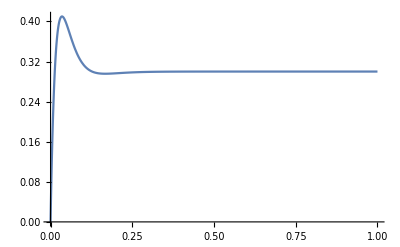

```mathematica
Plot[0.3(100t ⅇ^(-40t)+1-ⅇ^(-20t)),{t,0,1},PlotRange->All]
```

```mathematica
200t ⅇ^(-40t)+1-ⅇ^(-20t)/.t->1.5
```

1.

```mathematica
%71
```

False